```mathematica
(*plot mesh vertices*)
```

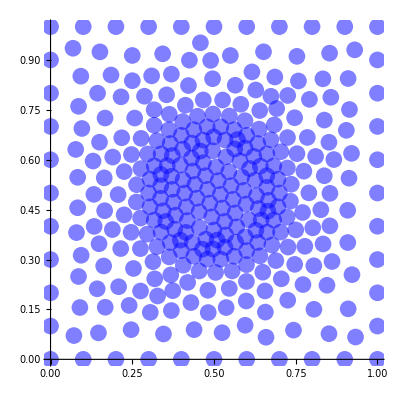

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square/shape_line/solution/mesh_0/vertices.csv"]
tabve=Table[{tabve[[i,2]],tabve[[i,3]]},{i,2,Length[tabve]}]
plotve=ListPlot[tabve,PlotStyle->{Blue,Opacity->0.5,PointSize->0.03},AspectRatio->1]
```

```mathematica
(*plot DOF coordinates*)
```

```mathematica
tabdof=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/two_domains/discontinuous/dofs.csv"];
tabdof=Table[{tabdof[[i,1]],tabdof[[i,2]]},{i,2,Length[tabdof]}]
plotdof=ListPlot[tabdof,PlotStyle->Red,AspectRatio->1]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/two_domains/discontinuous/dofs.csv not found during Import.

{}

-Graphics-

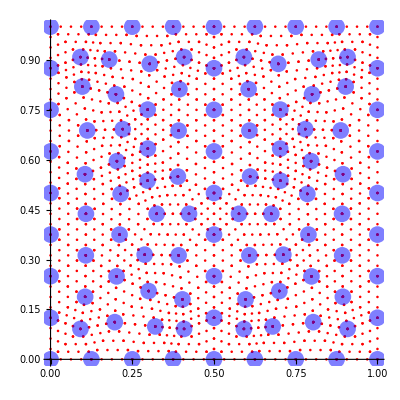

```mathematica
Show[plotdof,plotve]
```